# Verifications of integrals evaluation

## For comparison with integralARB package

## Overview of test cases

=== SUMMARY: All Test Functions ===

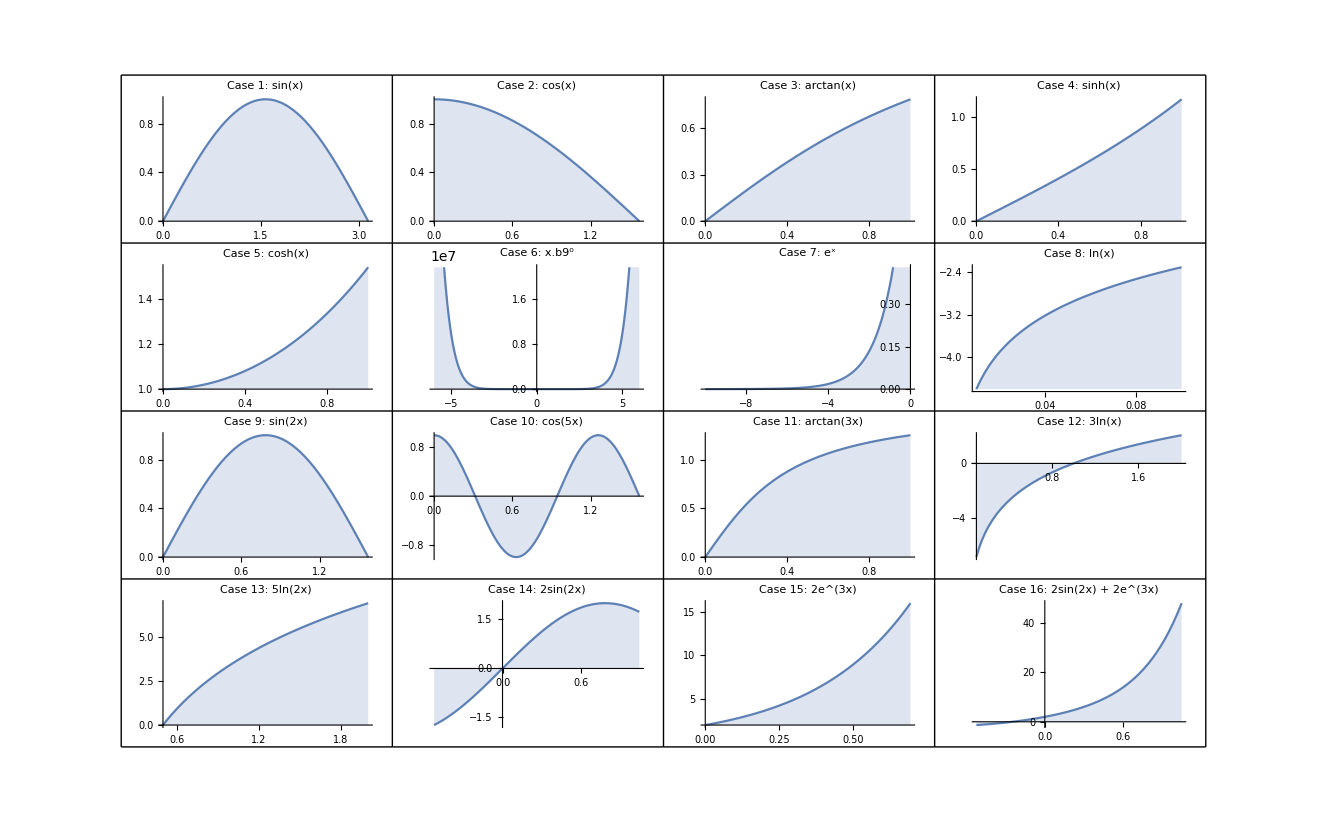

```mathematica
(* Create a summary plot showing all functions *)
Print["=== SUMMARY: All Test Functions ==="];
GraphicsGrid[{
  {Plot[Sin[x], {x, 0, Pi}, Filling -> Axis, PlotLabel -> "Case 1: sin(x)", ImageSize -> 200],
   Plot[Cos[x], {x, 0, Pi/2}, Filling -> Axis, PlotLabel -> "Case 2: cos(x)", ImageSize -> 200],
   Plot[ArcTan[x], {x, 0, 1}, Filling -> Axis, PlotLabel -> "Case 3: arctan(x)", ImageSize -> 200],
   Plot[Sinh[x], {x, 0, 1}, Filling -> Axis, PlotLabel -> "Case 4: sinh(x)", ImageSize -> 200]},
  {Plot[Cosh[x], {x, 0, 1}, Filling -> Axis, PlotLabel -> "Case 5: cosh(x)", ImageSize -> 200],
   Plot[x^10, {x, -6, 6}, Filling -> Axis, PlotLabel -> "Case 6: x.b9⁰", ImageSize -> 200],
   Plot[Exp[x], {x, -10, 0}, Filling -> Axis, PlotLabel -> "Case 7: eˣ", ImageSize -> 200],
   Plot[Log[x], {x, 0.01, 0.1}, Filling -> Axis, PlotLabel -> "Case 8: ln(x)", ImageSize -> 200]},
  {Plot[Sin[2*x], {x, 0, Pi/2}, Filling -> Axis, PlotLabel -> "Case 9: sin(2x)", ImageSize -> 200],
   Plot[Cos[5*x], {x, 0, Pi/2}, Filling -> Axis, PlotLabel -> "Case 10: cos(5x)", ImageSize -> 200],
   Plot[ArcTan[3*x], {x, 0, 1}, Filling -> Axis, PlotLabel -> "Case 11: arctan(3x)", ImageSize -> 200],
   Plot[3*Log[x], {x, 0.1, 2}, Filling -> Axis, PlotLabel -> "Case 12: 3ln(x)", ImageSize -> 200]},
  {Plot[5*Log[2*x], {x, 0.5, 2}, Filling -> Axis, PlotLabel -> "Case 13: 5ln(2x)", ImageSize -> 200],
   Plot[2*Sin[2*x], {x, -Pi/6, Pi/3}, Filling -> Axis, PlotLabel -> "Case 14: 2sin(2x)", ImageSize -> 200],
   Plot[2*Exp[3*x], {x, 0, Log[2]}, Filling -> Axis, PlotLabel -> "Case 15: 2e^(3x)", ImageSize -> 200],
   Plot[2*Sin[2*x] + 2*Exp[3*x], {x, -Pi/6, Pi/3}, Filling -> Axis, PlotLabel -> "Case 16: 2sin(2x) + 2e^(3x)", ImageSize -> 200]}
}, Frame -> All]
```

## Testing on September 10, 2025

We will test the precision of integralARB R package with 16 different integrals. The answer will range from integers to rational and irrational numbers to best evaluate the precision attainable by the package. With this Mathematica notebook, we will try to solve each integral symbolically before getting the decimal representation in high precision to minimize errors in computation.

Split the code by case.

=== Case 1: ∫ sin(x) dx ===

Symbolic result: 2

High precision value: 2.

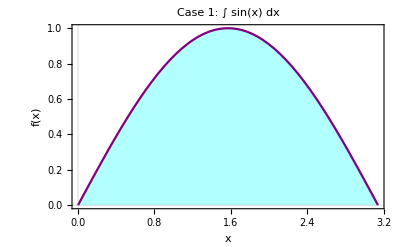

Exact value: 2.

=== Case 2: ∫ cos(x) dx ===

Symbolic result: 1

High precision value: 1.

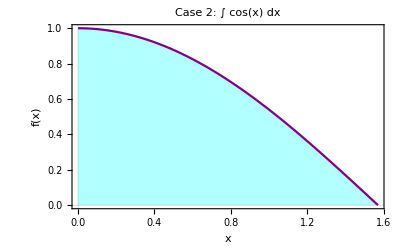

Exact value: 1.

=== Case 3: ∫ arctan(x) dx ===

Symbolic result: 1/4 (π-Log[4])

High precision value: 0.43882457311747565490704478509078743701154228266365

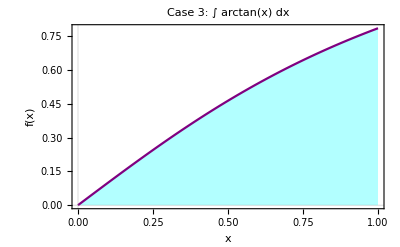

Exact value: 0.43882457311747565490704478509078743701154228266365

=== Case 4: ∫ sinh(x) dx ===

Symbolic result: -1+Cosh[1]

High precision value: 0.54308063481524377847790562075706168260152911236586

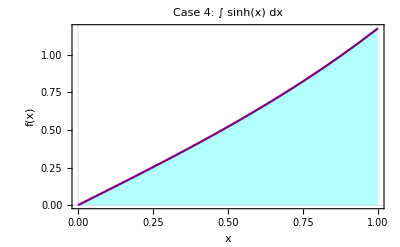

Exact value: 0.54308063481524377847790562075706168260152911236586

=== Case 5: ∫ cosh(x) dx ===

Symbolic result: Sinh[1]

High precision value: 1.1752011936438014568823818505956008151557179813341

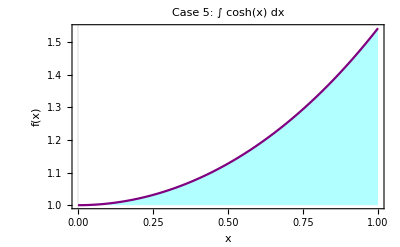

Exact value: 1.1752011936438014568823818505956008151557179813341

=== Case 6: ∫ x.b9⁰ dx ===

Symbolic result: 725594112/11

High precision value: 6.5963101090909090909090909090909090909090909090909×10^7

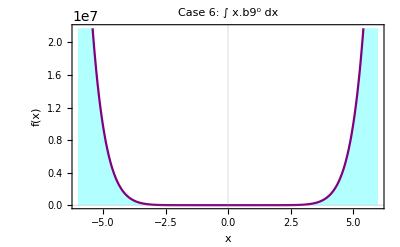

Exact value: 6.5963101090909090909090909090909090909090909090909×10^7

=== Case 7: ∫ eˣ dx ===

Symbolic result: 1-1/ⅇ^10

High precision value: 0.99995460007023751514846440848443944938976208191113

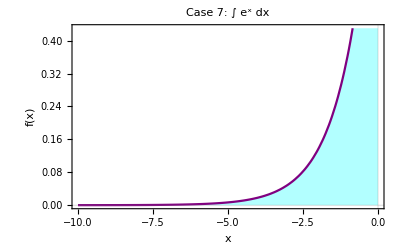

Exact value: 0.99995460007023751514846440848443944938976208191113

=== Case 8: ∫ ln(x) dx ===

Symbolic result: 1/100 (-9-8 Log[10])

High precision value: -0.2742068074395236547214393163747491366080881190903

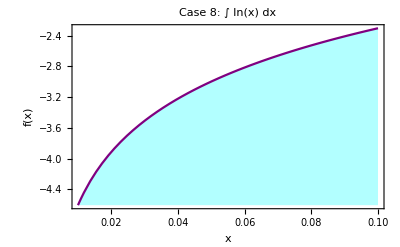

Exact value: -0.2742068074395236547214393163747491366080881190903

=== Case 9: ∫ sin(2x) dx ===

Symbolic result: 1

High precision value: 1.

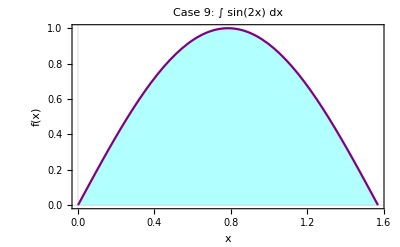

Exact value: 1.

=== Case 10: ∫ cos(5x) dx ===

Symbolic result: 1/5

High precision value: 0.2

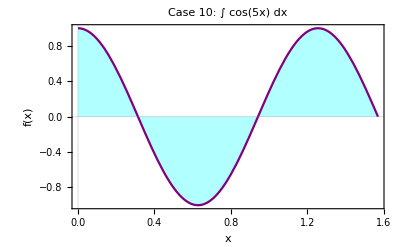

Exact value: 0.2

=== Case 11: ∫ arctan(3x) dx ===

Symbolic result: ArcTan[3]-Log[10]/6

High precision value: 0.86528159023258014516025183483369608847764582269177

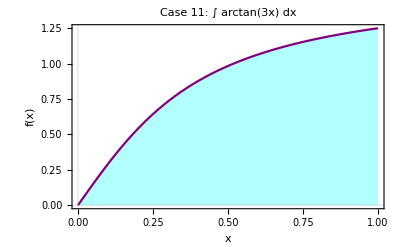

Exact value: 0.86528159023258014516025183483369608847764582269177

=== Case 12: ∫ 3ln(x) dx ===

Symbolic result: 3/10 (-19+10 Log[4]+Log[10])

High precision value: -0.85034138874211443829120983484563132926666874724984

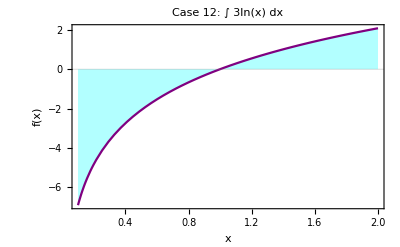

Exact value: -0.85034138874211443829120983484563132926666874724984

=== Case 13: ∫ 5ln(2x) dx ===

Symbolic result: 5 (-3/2+Log[16])

High precision value: 6.3629436111989061883446424291635313615100026872051

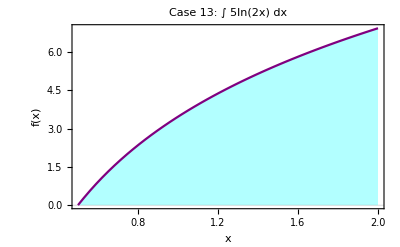

Exact value: 6.3629436111989061883446424291635313615100026872051

=== Case 14: ∫ 2sin(2x) dx ===

Symbolic result: 1

High precision value: 1.

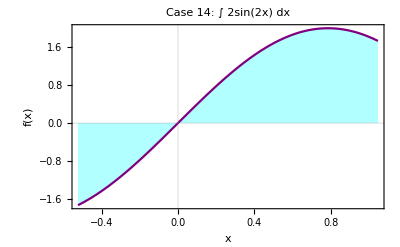

Exact value: 1.

=== Case 15: ∫ 2e^(3x) dx ===

Symbolic result: 14/3

High precision value: 4.6666666666666666666666666666666666666666666666667

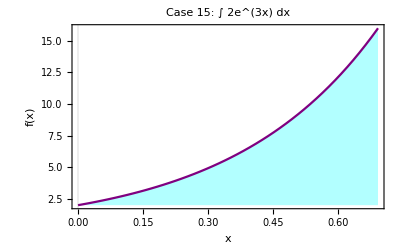

Exact value: 4.6666666666666666666666666666666666666666666666667

=== Case 16: ∫[2sin(2x) + 2e^(3x)] dx ===

Symbolic result: 1-(2 ⅇ^(-π/2))/3+(2 ⅇ^π)/3

High precision value: 16.288542037619004731454753832075712406821485600646

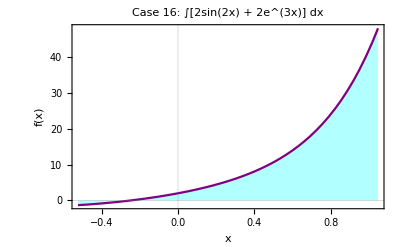

Exact value: 16.288542037619004731454753832075712406821485600646

```mathematica
(* Set high precision for calculations *)
$MaxExtraPrecision = 200;
precision = 50;

(* Function to compute integral symbolically first, then numerically if needed *)
computeIntegral[integrand_, var_, limits_, caseNum_, description_] := Module[
  {symbolic, exact, numerical, plot},
  
  Print["=== Case ", caseNum, ": ", description, " ==="];
  
  (* Try symbolic integration first *)
  symbolic = Quiet[Integrate[integrand, {var, limits[[1]], limits[[2]]}]];
  
  If[FreeQ[symbolic, Integrate],
    (* Symbolic integration succeeded *)
    exact = N[symbolic, precision];
    Print["Symbolic result: ", symbolic];
    Print["High precision value: ", exact],
    (* Symbolic failed, use high-precision numerical *)
    exact = NIntegrate[integrand, {var, limits[[1]], limits[[2]]}, 
           WorkingPrecision -> precision];
    Print["Symbolic integration failed, using numerical: ", exact]
  ];
  
  (* Create plot *)
  plot = Plot[integrand, {var, limits[[1]], limits[[2]]}, 
    PlotStyle -> Purple, 
    Filling -> Axis, 
    FillingStyle -> Opacity[0.3, Cyan],
    PlotLabel -> "Case " <> ToString[caseNum] <> ": " <> description,
    AxesLabel -> {ToString[var], "f(" <> ToString[var] <> ")"},
    PlotTheme -> "Scientific",
    ImageSize -> 400];
  
  Print[plot];
  Print["Exact value: ", exact];
  Print[];
  
  Return[exact]
];

(* Case 1: Simple integral - sin(x) *)
exact1 = computeIntegral[Sin[x], x, {0, Pi}, 1, "∫ sin(x) dx"];

(* Case 2: Simple integral - cos(x) *)
exact2 = computeIntegral[Cos[x], x, {0, Pi/2}, 2, "∫ cos(x) dx"];

(* Case 3: ArcTan integral *)
exact3 = computeIntegral[ArcTan[x], x, {0, 1}, 3, "∫ arctan(x) dx"];

(* Case 4: Sinh integral *)
exact4 = computeIntegral[Sinh[x], x, {0, 1}, 4, "∫ sinh(x) dx"];

(* Case 5: Cosh integral *)
exact5 = computeIntegral[Cosh[x], x, {0, 1}, 5, "∫ cosh(x) dx"];

(* Case 6: Polynomial integral *)
exact6 = computeIntegral[x^10, x, {-6, 6}, 6, "∫ x.b9⁰ dx"];

(* Case 7: Exponential integral *)
exact7 = computeIntegral[Exp[x], x, {-10, 0}, 7, "∫ eˣ dx"];

(* Case 8: Log integral *)
exact8 = computeIntegral[Log[x], x, {1/100, 1/10}, 8, "∫ ln(x) dx"];

(* Case 9: Chain rule - sin(2x) *)
exact9 = computeIntegral[Sin[2*x], x, {0, Pi/2}, 9, "∫ sin(2x) dx"];

(* Case 10: Chain rule - cos(5x) *)
exact10 = computeIntegral[Cos[5*x], x, {0, Pi/2}, 10, "∫ cos(5x) dx"];

(* Case 11: Chain rule - arctan(3x) *)
exact11 = computeIntegral[ArcTan[3*x], x, {0, 1}, 11, "∫ arctan(3x) dx"];

(* Case 12: Combined - 3*ln(x) *)
exact12 = computeIntegral[3*Log[x], x, {1/10, 2}, 12, "∫ 3ln(x) dx"];

(* Case 13: Combined - 5*ln(2x) *)
exact13 = computeIntegral[5*Log[2*x], x, {1/2, 2}, 13, "∫ 5ln(2x) dx"];

(* Case 14: Combined - 2*sin(2x) *)
exact14 = computeIntegral[2*Sin[2*x], x, {-Pi/6, Pi/3}, 14, "∫ 2sin(2x) dx"];

(* Case 15: Combined - 2*exp(3x) *)
exact15 = computeIntegral[2*Exp[3*x], x, {0, Log[2]}, 15, "∫ 2e^(3x) dx"];

(* Case 16: Combined - sum *)
exact16 = computeIntegral[2*Sin[2*x] + 2*Exp[3*x], x, {-Pi/6, Pi/3}, 16, 
  "∫[2sin(2x) + 2e^(3x)] dx"];
```

## Symbolic and 50-digit precision summary

```mathematica
(* ============================================================================ *)
(*           COMBINED TABLE: SYMBOLIC FORMS + 50-DIGIT PRECISION VALUES       *)
(* ============================================================================ *)

(* Define your colors *)
blueWhale = RGBColor[0.015, 0.223, 0.309];
yellowOrange = RGBColor[1, 0.729, 0.227];
lightGray = RGBColor[0.95, 0.95, 0.95];

(* Create combined data with both symbolic and numeric values *)
combinedTableData = {
  (* Header row *)
  {Style["Case", Bold, FontSize -> 14, FontColor -> Black], 
   Style["Exact Symbolic Result", Bold, FontSize -> 14, FontColor -> Black], 
   Style["50-Digit Precision Value", Bold, FontSize -> 14, FontColor -> Black]}
};

(* Define symbolic results (using exact bounds for cases 8, 12, 13) *)
symbolicResults = {
  Integrate[Sin[x], {x, 0, Pi}],
  Integrate[Cos[x], {x, 0, Pi/2}],
  Integrate[ArcTan[x], {x, 0, 1}],
  Integrate[Sinh[x], {x, 0, 1}],
  Integrate[Cosh[x], {x, 0, 1}],
  Integrate[x^10, {x, -6, 6}],
  Integrate[Exp[x], {x, -10, 0}],
  Integrate[Log[x], {x, 1/100, 1/10}],  (* Fixed: exact bounds *)
  Integrate[Sin[2*x], {x, 0, Pi/2}],
  Integrate[Cos[5*x], {x, 0, Pi/2}],
  Integrate[ArcTan[3*x], {x, 0, 1}],
  Integrate[3*Log[x], {x, 1/10, 2}],     (* Fixed: exact bounds *)
  Integrate[5*Log[2*x], {x, 1/2, 2}],    (* Fixed: exact bounds *)
  Integrate[2*Sin[2*x], {x, -Pi/6, Pi/3}],
  Integrate[2*Exp[3*x], {x, 0, Log[2]}],
  Integrate[2*Sin[2*x] + 2*Exp[3*x], {x, -Pi/6, Pi/3}]
};

(* Add data rows *)
Do[
  AppendTo[combinedTableData, {
    Style[ToString[i], FontSize -> 12, FontWeight -> Bold],
    Style[symbolicResults[[i]], FontSize -> 10],
    Style[NumberForm[ToExpression["exact" <> ToString[i]], {50, 45}], 
          FontSize -> 9, FontFamily -> "Courier"]
  }],
  {i, 1, 16}
];

(* Create the professional grid *)
combinedGrid = Grid[combinedTableData,
  (* Alternating row colors with header *)
  Background -> {None, 
    Join[{yellowOrange}, 
         Table[If[EvenQ[i], lightGray, White], {i, 1, 16}]]},
  
  (* Borders and dividers *)
  Dividers -> {{True, {False}, True}, {True, True, {False}, True}},
  
  (* Spacing and alignment *)
  Spacings -> {2, 1.5},
  Alignment -> {{Center, Left, Left}, Center},
  
  (* Frame styling *)
  Frame -> All,
  FrameStyle -> Directive[Thick, blueWhale],
  
  (* Column widths *)
  ItemSize -> {{6, 25, 30}, Automatic}
];

(* Display the table *)
Print[Style["=== integralARB REFERENCE TABLE ===", 
            Bold, FontSize -> 16, FontColor -> blueWhale]];
Print[""];
combinedGrid

(* Export options *)
Print[""];
Print[Style["=== EXPORT OPTIONS ===", Bold, FontSize -> 14, FontColor -> blueWhale]];
Print["• Combined table: Export[\"reference_table.pdf\", combinedGrid]"];
Print["• High resolution: Export[\"reference_table.png\", combinedGrid, ImageResolution -> 300]"];
Print["• Data only: Export[\"reference_data.csv\", combinedTableData]"];
Print["• Excel format: Export[\"reference_data.xlsx\", combinedTableData]"];

(* Quick verification table *)
Print[""];
Print[Style["=== VERIFICATION SUMMARY ===", Bold, FontSize -> 14, FontColor -> blueWhale]];

verificationData = Join[
  {{Style["Case", Bold, FontColor -> Black], 
    Style["Status", Bold, FontColor -> Black], 
    Style["Value", Bold, FontColor -> Black]}},
  Table[
    Module[{val, status},
      val = ToExpression["exact" <> ToString[i]];
      status = If[NumericQ[N[val]], 
        Style["✓ Verified", FontColor -> Darker[Green]], 
        Style["✗ Error", FontColor -> Red]];
      {ToString[i], status, NumberForm[N[val, 50], 45]}
    ], {i, 1, 16}]
];

Grid[verificationData,
  Background -> {None, Join[{yellowOrange}, Table[White, {i, 1, 16}]]},
  Frame -> All,
  FrameStyle -> blueWhale,
  Spacings -> {1.5, 1},
  Alignment -> Center,
  ItemSize -> {{4, 10, 25}, Automatic}
]
```

=== integralARB REFERENCE TABLE ===

Case | Exact Symbolic Result | 50-Digit Precision Value
1 | 2 | 2.000000000000000000000000000000000000000000000
2 | 1 | 1.000000000000000000000000000000000000000000000
3 | 1/4 (π-Log[4]) | 0.438824573117475654907044785090787437011542283
4 | -1+Cosh[1] | 0.543080634815243778477905620757061682601529112
5 | Sinh[1] | 1.175201193643801456882381850595600815155717981
6 | 725594112/11 | 6.596310109090909090909090909090909090909090909×10^7
7 | 1-1/ⅇ^10 | 0.999954600070237515148464408484439449389762082
8 | 1/100 (-9-8 Log[10]) | -0.274206807439523654721439316374749136608088119
9 | 1 | 1.000000000000000000000000000000000000000000000
10 | 1/5 | 0.200000000000000000000000000000000000000000000
11 | ArcTan[3]-Log[10]/6 | 0.865281590232580145160251834833696088477645823
12 | 3/10 (-19+10 Log[4]+Log[10]) | -0.850341388742114438291209834845631329266668747
13 | 5 (-3/2+Log[16]) | 6.362943611198906188344642429163531361510002687
14 | 1 | 1.000000000000000000000000000000000000000000000
15 | 14/3 | 4.666666666666666666666666666666666666666666667
16 | 1-(2 ⅇ^(-π/2))/3+(2 ⅇ^π)/3 | 16.288542037619004731454753832075712406821485601

=== EXPORT OPTIONS ===

• Combined table: Export["reference_table.pdf", combinedGrid]

• High resolution: Export["reference_table.png", combinedGrid, ImageResolution -> 300]

• Data only: Export["reference_data.csv", combinedTableData]

• Excel format: Export["reference_data.xlsx", combinedTableData]

=== VERIFICATION SUMMARY ===

Case | Status | Value
1 | ✓ Verified | 2.00000000000000000000000000000000000000000000
2 | ✓ Verified | 1.00000000000000000000000000000000000000000000
3 | ✓ Verified | 0.438824573117475654907044785090787437011542283
4 | ✓ Verified | 0.543080634815243778477905620757061682601529112
5 | ✓ Verified | 1.17520119364380145688238185059560081515571798
6 | ✓ Verified | 6.59631010909090909090909090909090909090909091×10^7
7 | ✓ Verified | 0.999954600070237515148464408484439449389762082
8 | ✓ Verified | -0.274206807439523654721439316374749136608088119
9 | ✓ Verified | 1.00000000000000000000000000000000000000000000
10 | ✓ Verified | 0.200000000000000000000000000000000000000000000
11 | ✓ Verified | 0.865281590232580145160251834833696088477645823
12 | ✓ Verified | -0.850341388742114438291209834845631329266668747
13 | ✓ Verified | 6.36294361119890618834464242916353136151000269
14 | ✓ Verified | 1.00000000000000000000000000000000000000000000
15 | ✓ Verified | 4.66666666666666666666666666666666666666666667
16 | ✓ Verified | 16.2885420376190047314547538320757124068214856

```mathematica
Export["/Users/khuetran/integralARB/mathematica_reference_table.pdf", combinedGrid]
```

/Users/khuetran/integralARB/mathematica_reference_table.pdf